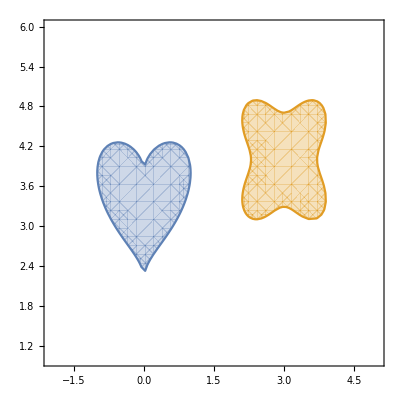

```mathematica
mapa =RegionPlot[{x^2+(5(y-3)/4-Sqrt[Abs[x]])^2 ≤ 1,(2(x-3)^2+2(y-4)^2)^3-40(x-3)^2 *(y-4)^2 ≤ 1},{x,-2,5},{y,1,6}]
```

```mathematica
g1=x1^2+(5(x2-3)/4-(x1^2+0.001^2)^(1/4))^2;
g2=(2(y1-3)^2+2(y2-4)^2)^3-40(y1-3)^2 *(y2-4)^2;
f = (x1-y1)^2 + (x2-y2)^2;
smallLagrangian= Piecewise[{{-λ^2 /(2ρ),λ+ρ*g ≤ ρ},{λ(g-1)+ρ/2 (g-1)^2,λ+ρ*g > ρ}}]
```

Piecewise[{{-λ^2/(2 ρ), λ+g ρ≤ρ}, {(-1+g) λ+1/2 (-1+g)^2 ρ, λ+g ρ>ρ}, {0, True}}]

```mathematica
Lagrangian = f + ReplaceAll[ReplaceAll[smallLagrangian,g->g1],λ->λ1]+ReplaceAll[ReplaceAll[smallLagrangian,g->g2],λ->λ2]
```

(x1-y1)^2+(x2-y2)^2+(Piecewise[{{-λ1^2/(2 ρ), λ1+(x1^2+(-(1.×10^-6+x1^2)^(1/4)+5/4 (-3+x2))^2) ρ≤ρ}, {(-1+x1^2+(-(1.×10^-6+x1^2)^(1/4)+5/4 (-3+x2))^2) λ1+1/2 (-1+x1^2+(-(1.×10^-6+x1^2)^(1/4)+5/4 (-3+x2))^2)^2 ρ, λ1+(x1^2+(-(1.×10^-6+x1^2)^(1/4)+5/4 (-3+x2))^2) ρ>ρ}, {0, True}}])+(Piecewise[{{-λ2^2/(2 ρ), λ2+((2 (-3+y1)^2+2 (-4+y2)^2)^3-40 (-3+y1)^2 (-4+y2)^2) ρ≤ρ}, {(-1+(2 (-3+y1)^2+2 (-4+y2)^2)^3-40 (-3+y1)^2 (-4+y2)^2) λ2+1/2 (-1+(2 (-3+y1)^2+2 (-4+y2)^2)^3-40 (-3+y1)^2 (-4+y2)^2)^2 ρ, λ2+((2 (-3+y1)^2+2 (-4+y2)^2)^3-40 (-3+y1)^2 (-4+y2)^2) ρ>ρ}, {0, True}}])

```mathematica
DfDx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2}} ];
D2fDxx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2},2} ];
ρ=1;
```

```mathematica
{x1,x2,y1,y2,λ1,λ2}={1.,4.,2.,3.,0.,0.}
i=0;
history={{x1,x2,y1,y2}};
While[ Sqrt[DfDx.DfDx]>10^-12&&i≤15,
dx=-Inverse[D2fDxx].DfDx;
{x1,x2,y1,y2,λ1,λ2}={x1,x2,y1,y2,λ1,λ2}+dx;
AppendTo[ history,{x1,x2,y1,y2} ];
i=i+1;
Print[ "i=",i," xy=",{x1,x2,y1,y2,λ1,λ2}," |Δu|=",Sqrt[dx.dx]," |DfDu|=",Sqrt[DfDx.DfDx] ]
]//Timing
```

{1.,4.,2.,3.,0.,0.}

i=1 xy={1.37211,2.8581,2.1019,3.10345,0.825468,1.52688} |Δu|=2.11572 |DfDu|=164.593

i=2 xy={1.16472,3.41977,2.15916,3.16638,0.792551,1.05414} |Δu|=0.768308 |DfDu|=53.0465

i=3 xy={1.00972,3.58088,2.17289,3.19633,0.978001,0.270486} |Δu|=0.836401 |DfDu|=9.46046

i=4 xy={0.967715,3.58197,2.14111,3.2384,1.06492,0.0444931} |Δu|=0.251341 |DfDu|=1.90184

i=5 xy={0.982255,3.63515,2.05523,3.39567,0.993215,0.0483698} |Δu|=0.20077 |DfDu|=8.57366

i=6 xy={0.983325,3.64734,2.0969,3.41045,1.03533,0.112672} |Δu|=0.0895193 |DfDu|=2.44587

i=7 xy={0.986421,3.66241,2.10456,3.44636,1.04537,0.0785515} |Δu|=0.0533848 |DfDu|=0.423513

i=8 xy={0.988816,3.67557,2.10949,3.47806,1.05303,0.0777248} |Δu|=0.0355978 |DfDu|=0.126603

i=9 xy={0.989074,3.67766,2.11147,3.48309,1.05567,0.0784686} |Δu|=0.0064232 |DfDu|=0.00522044

i=10 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δu|=0.000290167 |DfDu|=9.94479×10^-6

i=11 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δu|=5.67082×10^-7 |DfDu|=2.95114×10^-11

i=12 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δu|=1.80689×10^-12 |DfDu|=4.32679×10^-14

{0.015625,Null}

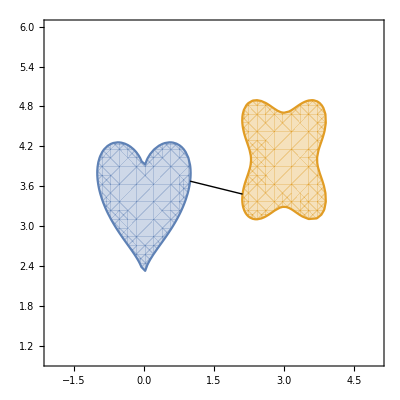

```mathematica
Show[mapa,Graphics[Line[{{0.9890878469951829,3.6777618072114286},{2.1115474918375594,3.483330697082046}}],Point[{{0.9890878469951829,3.6777618072114286},{2.1115474918375594,3.483330697082046}}]]]
```